```mathematica
(*72 Hz e Subscript[V, 0]=0,5 V*)
```

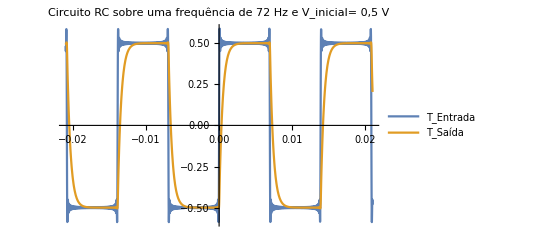

```mathematica
Plot[{Sum[(4*0.5)/(n π)Sin[2*72π n t],{n,1,100,2}], Sum[(4*0.5)/(n π √(1+((n 72)/338)^2))Sin[2*72π n t  + ArcTan[-(n 72)/338]],{n,1,100,2}]},{t,-0.021,0.021},Exclusions->None,PlotLegends->{Subscript[T, Entrada], Subscript[T, Saída] },PlotLabel->"Circuito RC sobre uma frequência de 72 Hz e V_inicial= 0,5 V"]
```

```mathematica
(*360 Hz e Subscript[V, 0]= -0,5*)
```

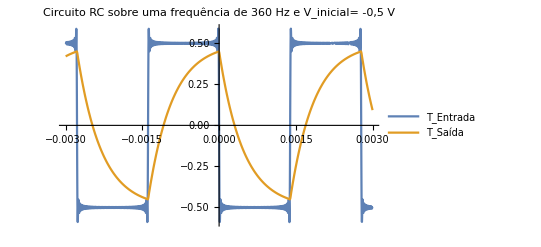

```mathematica
Plot[{Sum[(-4*0.5)/(n π)Sin[2*360π n t],{n,1,100,2}],Sum[(-4*0.5)/(n π √(1+((n 360)/338)^2))Sin[2*360π n t  + ArcTan[-(n 360)/338]],{n,1,100,2}]},{t,-0.003,0.003},Exclusions->None,PlotLegends->{Subscript[T, Entrada], Subscript[T, Saída] },PlotLabel->"Circuito RC sobre uma frequência de 360 Hz e V_inicial= -0,5 V"]
```

```mathematica
(*7200 Hz e Subscript[V, 0]=0.5*)
```

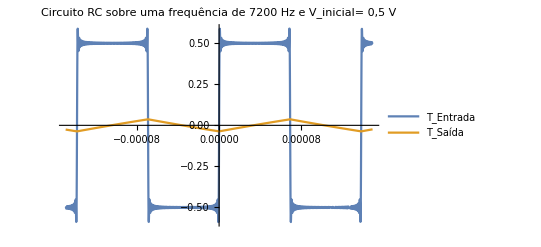

```mathematica
Plot[{Sum[(4*0.5)/(n π)Sin[2*7200π n t],{n,1,100,2}],Sum[(4*0.5)/(n π √(1+((n 7200)/338)^2))Sin[2*7200π n t  + ArcTan[-(n 7200)/338]],{n,1,100,2}]},{t,-0.00015,0.00015},Exclusions->None,PlotLegends->{Subscript[T, Entrada], Subscript[T, Saída] },PlotLabel->"Circuito RC sobre uma frequência de 7200 Hz e V_inicial= 0,5 V"]
```